# Colorful-色彩科学计算框架

## 变量设置：g_

### 目录设置

```mathematica
(*gCSDir：当前框架所在目录*)
gCSDir=NotebookDirectory[];
(*设置导入导出默认路径：Workspace*)
SetDirectory[gCSDir<>"Workspace/"];
```

### 其他全局设置

```mathematica
(*绘图大小*)
gDrawingSize=800;
(*LAB、LUV计算中，用Y计算L的参考Y值。默认为1。暂设为全局参数。修改的意义不大*)
gRefY=1;
```

## 色度学函数&数据导入

### XYZ数据导入与处理

#### 基础函数定义

```mathematica
(*XYZ和xyY的转换函数。
Note：不能处理0分母*)
XYZ2xyY[{X_,Y_,Z_}]:={X/(X+Y+Z),Y/(X+Y+Z),Y}
xyY2XYZ[{x_,y_,Y_}]:=
(*若亮度为0，则输出全为0*)
If[Y==0,{0,0,0},
(*y==0而Y不等于0，说明X或Z非常大，这在实际计算中不可能发生*)
If[y==0,{0,0,0},
{x/y*Y,Y,(1-x-y)/y*Y}]]
```

```mathematica
(*在Colorful里，用69维向量逼近光谱分布函数，所以必须造轮子做一个类似于函数归一化的“列表归一化” —— 使列表的第n层之和等于S*)
iListSum[l_,S_]:=S*l/Total[l,Infinity]
ListNorm[l_,S_,n_:0]:=If[n==0,iListSum[l,S],Map[iListSum[#,S]&,l,n]]
```

```mathematica
(*相对值处理，用于XYZ->xyz或RGB->rgb*)
Relative[Pixel_]:=Map[Function[{x},{x[[1]]/(x[[1]]+x[[2]]+x[[3]]),x[[2]]/(x[[1]]+x[[2]]+x[[3]]),x[[3]]/(x[[1]]+x[[2]]+x[[3]])}],
{Pixel}]
```

```mathematica
(*使列表中所有小于0的值设为0*)
Clip0[l_]:=If[l<0,0,l]
SetAttributes[Clip0,Listable]
```

#### 导入数据：以XYZ坐标表示的色匹配函数CMFXYZ

```mathematica
(*
这里使用CIE1931-2Deg的数据，波长范围为380-720。此处可以任选数据集，但波长范围的调整还有点麻烦。
数据来源于Bruce lindbloom
*)
rawDataCMFXYZ=Import[gCSDir<>"/Data/Colorimetry/1931-2d-5nm-380-720.csv"];
rawDataFrequencyRange = rawDataCMFXYZ[[All,1]];
```

```mathematica
(*这里定义全局波长范围，为一个69x1的列向量*)
FrequencyRange=rawDataFrequencyRange;
(*检查向量维度，确定是69*1*)
Dimensions[%]
```

{69}

```mathematica
(*一个标准的色匹配函数Color Matching Function是3x69的矩阵。
这里的处理非常重要：
①使色匹配函数每一通道各自的和相等：保证标准E光源的X=Y=Z；
②保证每一通道各自的和为1：保证每5nm波长强度都为1的E光源{1,1,1,...,1}算出的结果为X=Y=Z=1
*)
CMFXYZ=ListNorm[Transpose[rawDataCMFXYZ[[All,2;;4]]],1,1];
(*检查向量维度*)
Dimensions[%]
```

{3,69}

```mathematica
(*测试。先建立一个E光源，再与XYZ色匹配方程相乘，得出X=Y=Z=1*)
Table[1,{x,1,69}]
CMFXYZ.Table[1,{x,1,69}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{1.,1.,1.}

## 色彩管理：CM_

### 色彩转换工具

#### 色彩空间数据库

```mathematica
(*
白点的标准不多，可以全部列举如下。为了方便计算，不用xy定义。
如果想添加白点，可以用xyY2XYZ函数和白点的xy数据计算，Y设为1。
数据来源于Bruce lindbloom。原网页注释：
All come from ASTM E308-01 except B which comes from Wyszecki& Stiles,p.769
*)
WPs=Association[{
"A"->{1.09850,1.00000,0.35585},
"B"->{0.99072,1.00000,0.85223},
"C"->{0.98074,1.00000,1.18232},
"D50"->{0.96422,1.00000,0.82521},
"D55"->{0.95682,1.00000,0.92149},
"D65"->{0.95047,1.00000,1.08883},
"D75"->{0.94972,1.00000,1.22638},
"E"->{1.00000,1.00000,1.00000},
"F2"->{0.99186,1.00000,0.67393},
"F7"->{0.95041,1.00000,1.08747},
"F11"->{1.00962,1.00000,0.64350},
"ACESD60"->{0.95265,1,1.00883}(*AP0\AP1\P3-ACES所用白点*)
}];
```

```mathematica
(*色彩空间的基色大多用xy来定义，故此处使用xy坐标*)
ColorSpacePrixy=Association[{
(*这里存储着每个基色的xyY
数据补充：http://www.brucelindbloom.com/index.html?WorkingSpaceInfo.html
这里处理得不够漂亮，可能需要重新写。
*)
"AdobeRGB"->{{0.6400,0.3300},{ 0.2100 ,0.7100},{ 0.1500,0.0600}},
"ProPhotoRGB"->{{0.734699,0.265301},{0.159597,0.840403},{0.036598,0.000105}},
"sRGB"-> {{0.6400,0.3300},{ 0.3000,0.6000},{ 0.1500,0.0600}},
"709"-> {{0.6400,0.3300},{ 0.3000,0.6000},{ 0.1500,0.0600}},

"P3"->{{0.680,0.320},{0.265,0.690},{0.150,0.060}},
"2020"->{{0.708,0.292},{0.17,0.797},{0.131,0.046}},
"AP0"->{{0.7347,0.2653},{0.0000,1.0000},{0.0001,-0.0770}},
(*几个自用的色彩空间*)
"CrystalRGB"->{{0.65,0.337},{0.22,0.73},{0.138,0.038}},
"CrystalRGB2Adobe"->{{0.650,0.33},{0.22,0.73},{0.140,0.05}},
"CrystalRGBPG1.3"->{{0.57,0.346},{0.235,0.63},{0.150,0.09}},
"Pro400RGB"->{{0.659,0.341},{0.275,0.691},{0.145,0.0245}},
(*几个用于检查的色彩空间*)
"SmallRGB"->{{0.53,0.34},{0.25,0.5},{0.17,0.1}}
}];
```

#### 白平衡：Chromatic Adaptation

```mathematica
(*淘汰：这里之后会重写，加入Bradford、Von Kries方法
XYZScaling[XYZPixel_,iWP_,oWP_]:=XYZPixel*WPs[oWP]/WPs[iWP]
*)
```

```mathematica
CAMXYZScaling=CM1;
CAMBradford=
{{0.8951000,0.2664000,-0.1614000},
{-0.7502000,1.7135000,0.0367000},
{0.0389000,-0.0685000,1.0296000}};
CAMVonKries=
{{0.4002400,0.7076000,-0.0808100},{-0.2263000,1.1653200,0.0457000},0.0000000,0.0000000,0.9182200};
```

```mathematica
Options[ChromaticAdaptation]={
"Method"->"Bradford"
};
ChromaticAdaptation[XYZPixel_,iWP_,oWP_,OptionsPattern[]]:=Module[{MA,iρ,oρ},
MA=Piecewise[{
{CAMXYZScaling,OptionValue["Method"]== "XYZScaling"},
{CAMBradford,OptionValue["Method"]=="Bradford"},
{CAMVonKries,OptionValue["Method"]=="VonKries"}
},CAMBradford];
iρ=MA.(WPs[iWP]);
oρ=MA.(WPs[oWP]);
Inverse[MA].(CM1(oρ/iρ)).MA.XYZPixel
]
```

#### 空间转换矩阵：临时使用，逐渐淘汰

```mathematica
(*单位阵*)
CM1=IdentityMatrix[3];
```

```mathematica
(*XYZ与各种色彩空间转换。
此处所有的色彩矩阵自带白点转换，按原色彩空间的白点为参考
注：转换后，会出现负值和大于1的数，即超出色域的数据，使用Clip函数解决。*)
CMXYZ2sRGB={{3.2404542,-1.5371385,-0.4985314},{-0.9692660,1.8760108,0.0415560},{0.0556434,-0.2040259,1.0572252}};
CMsRGB2XYZ={{0.4124564,0.3575761,0.1804375},{0.2126729,0.7151522,0.0721750},{0.0193339,0.1191920,0.9503041}};
CMXYZ2AdobeRGB={{2.0413690,-0.5649464,-0.3446944},{-0.9692660,1.8760108,0.0415560},{0.0134474,-0.1183897,1.0154096}};
CMAdobeRGB2XYZ={{0.5767309,0.1855540,0.1881852},{0.2973769,0.6273491,0.0752741},{0.0270343,0.0706872,0.9911085}};
CMCIERGB2XYZ={{0.49000,0.31000,0.20000},{0.17697,0.81249,0.01063},{0.00000,0.01000,0.99000}}/0.17697;
Crystal2XYZ={{0.4884289,0.2687602,0.1932395},{0.2414816,0.7045658,0.0539526},{0.0133224,0.0815332,0.9940447}}
```

{{0.488429,0.26876,0.19324},{0.241482,0.704566,0.0539526},{0.0133224,0.0815332,0.994045}}

#### 空间转换函数：重要，且推荐使用，而不是用矩阵做。 基本的想法是，基色、白点和gamma各自设定，以获得最大的灵活性。这里的函数只做基色和白点的变换，gamma的变换根据需要手动做。

```mathematica
(*极其重要的函数，从xy与白点解出色彩空间基色的XYZ坐标*)
PriWp2XYZPrimaries[xyPrimaries_,Wp_]:=Module[{tempXYZPris},
tempXYZPris=If[xyPrimaries=="XYZ",CM1,
Transpose[xyY2XYZ/@(Append[#,1]&/@ColorSpacePrixy[xyPrimaries])]];
Transpose[
tempXYZPris.(CM1*LinearSolve[tempXYZPris,WPs[Wp]])
]
]
```

```mathematica
(*从XYZ转到特定空间,默认转到sRGB D65*)
Options[CMXYZ2CS]={
"oPri"->"sRGB",
"oWP"->"D65"};
CMXYZ2CS[pixel_,OptionsPattern[]]:=pixel.Inverse[
PriWp2XYZPrimaries[OptionValue["oPri"],OptionValue["oWP"]]
]
(*从特定空间转到XYZ，默认的特定空间是孙RGB D65*)
Options[CMCS2XYZ]={
"iPri"->"sRGB",
"iWP"->"D65"};
CMCS2XYZ[pixel_,OptionsPattern[]]:=pixel.PriWp2XYZPrimaries[OptionValue["iPri"],OptionValue["iWP"]]
```

```mathematica
(*任意空间转到任意空间的转换函数。
选项Clip是指，从广色域空间转到小色域空间时，超过1和低于0的数据是否被截掉，因为是研究用而非实际做色彩管理，所以默认不截掉！这样多次色彩管理不会损失数据。*)
Options[CM]={
"iPri"->"sRGB",
"oPri"->"sRGB",
"iWP"->"D65",
"oWP"->"D65",
"Clip"->False};
CM[pixel_,OptionsPattern[]]:=
If[OptionValue["Clip"],
Clip[CMXYZ2CS[CMCS2XYZ[pixel,
"iPri"->OptionValue["iPri"],
"iWP"->OptionValue["iWP"]
],
"oPri"->OptionValue["oPri"],
"oWP"->OptionValue["oWP"]],{0,1}],
CMXYZ2CS[CMCS2XYZ[pixel,
"iPri"->OptionValue["iPri"],
"iWP"->OptionValue["iWP"]
],
"oPri"->OptionValue["oPri"],
"oWP"->OptionValue["oWP"]]
]
```

```mathematica
(*测试：把D65白点的XYZ扔给色彩管理函数，转换到sRGB D65，结果应当是{1，1，1}
注意，XYZ空间的白点是“E”。
*)
CM[{0.95047,1.00000,1.08883},
"iPri"->"XYZ",
"iWP"->"E",
"oPri"->"sRGB",
"oWP"->"D65",
"Clip"->True]
```

{1.,1.,1.}

```mathematica
(*如果仅做 XYZ <-> CS 的转换，也可以单独使用CMCS2XYZ或CMXYZ2CS，上面测试的等价转换是：*)
```

```mathematica
CMXYZ2CS[{0.95047,1.00000,1.08883},"oPri"->"sRGB","oWP"->"D65"]
(*值得注意的是，单独使用CMCS2XYZ或CMXYZ2CS，没有Clip功能，无法截掉超过色域的数据*)
```

{1.,1.,1.}

## LAB支持：与白点有关

### XYZ <-> L*a*b*(白点相关)互换。 为了书写方便，并与LUV统一，L*a*b*命名为LAB，即为CIELAB坐标。

#### 转换函数定义

```mathematica
(*重要私有函数ifL，LAB与LUV共用。因为是用来计算L的，所以如此命名。
此处选择的常数并非CIE提供的标准近似数，而是一个并非标准但精确的分数，以期在大量转换时保持精度。
详情了解http://brucelindbloom.com/index.html?Eqn_ChromAdapt.html*)
ifL[x_]:=If[x>216/24389,
x^(1/3),
841/108 x+4/29
]
```

```mathematica
(*私有函数：从Y计算L。
这里的gRefY默认为1，意味着Y=1时，L=100。暂设为全局参数，不支持在调用上层函数时修改。*)
iY2L[Y_]:=116*ifL[Y/gRefY]-16
(*私有函数：从L计算Y*)
iL2Y[L_]:=gRefY*If[L>216/27,
((L+16)/116)^3,
(27L)/24389]
```

#### XYZ <-> LAB

```mathematica
Options[XYZ2LAB]={"refWP"->"D65"};
XYZ2LAB[{X_,Y_,Z_},OptionsPattern[]]:=Module[{fY,refWPXYZ},
fY=ifL[Y];
refWPXYZ=WPs[OptionValue["refWP"]];
{116fY-16,
500(ifL[X/refWPXYZ[[1]]]-fY),
200(fY-ifL[Z/refWPXYZ[[3]]])
}
]
```

```mathematica
(*LAB到XYZ的转换，
默认白点D65
*)
Options[LAB2XYZ]={"refWP"->"D65"};
LAB2XYZ[{L_,A_,B_},OptionsPattern[]]:=Module[{X,Y,Z,fx,fy,fz,refWPXYZ},
refWPXYZ=WPs[OptionValue["refWP"]];
fy=(L+16)/116;
fx=A/500+fy;
fz=fy-B/200;
Y=iL2Y[L];
X=refWPXYZ[[1]]*If[fx^3>216/24389,
fx^3,
108/841 fx-432/24389];
Z=refWPXYZ[[3]]*If[fz^3>216/24389,
fz^3,
108/841 fz-432/24389];
{X,Y,Z}]
```

```mathematica
(*套娃测试,结果等于输入，则测试成功*)
XYZ2LAB[LAB2XYZ[{1,1,1},"refWP"->"E"],"refWP"->"E"]
```

{1,1.,1.}

## LUV支持：LUV与白点有关，Luv与白点无关

### XYZ <-> L*u’v’(绝对坐标) <-> L*u*v*(白点相关)互换。 为了书写方便， 将绝对坐标L*u’v’命名为Luv，此即为CIE 1976 UCS坐标 将相对坐标L*u*v*命名为LUV，此即为CIELUV坐标。

#### L、u、v的产生和Luv <-> LUV

在LAB支持中已经定义了Y -> L转换的私有函数：iY2L。

```mathematica
(*私有函数：从XYZ计算u' v'，即CIE 1976 UCS图*)
iXYZ2uv[{X_,Y_,Z_}]:={4X/(X+15Y+3Z),9Y/(X+15Y+3Z)}
```

```mathematica
(*Luv到LUV的转换，
默认白点为D65；
*)
Options[Luv2LUV]={"refWP"->"D65"};
Luv2LUV[{L_,u_,v_},OptionsPattern[]]:=Module[{wpuv,uv},
wpuv=iXYZ2uv[WPs[OptionValue["refWP"]]];
uv={u,v};
Prepend[13L*(uv-wpuv),L]
]

(*LUV到Luv的转换，
默认白点为D65
*)
Options[LUV2Luv]={"refWP"->"D65"};
LUV2Luv[{L_,U_,V_},OptionsPattern[]]:=Module[{wpuv,uv},
wpuv=iXYZ2uv[WPs[OptionValue["refWP"]]];
uv={U/(13L),V/(13L)}+wpuv;
Prepend[uv,L]
]
```

#### XYZ <-> Luv/LUV

```mathematica
(*XYZ到Luv的转换。
*)
XYZ2Luv[{X_,Y_,Z_}]:=Prepend[iXYZ2uv[{X,Y,Z}],iY2L[Y]]
```

```mathematica
(*XYZ到LUV的转换，
默认白点为D65；
*)
Options[XYZ2LUV]={"refWP"->"D65"};
XYZ2LUV[{X_,Y_,Z_},OptionsPattern[]]:=Module[{l,wpuv},
l=iY2L[Y];
wpuv=iXYZ2uv[WPs[OptionValue["refWP"]]];
Prepend[13l*(iXYZ2uv[{X,Y,Z}]-wpuv),iY2L[Y]]
]
```

```mathematica
(*Luv到XYZ的转换*)
Luv2XYZ[{L_,u_,v_}]:=Module[{X,Y,Z},
Y=iL2Y[L];
X=Y*9u/(4v);
Z=Y*(12-3u-20v)/(4v);
{X,Y,Z}
]
```

```mathematica
(*LUV到XYZ的转换，
默认白点为D65
*)
Options[LUV2XYZ]={"refWP"->"D65"};
LUV2XYZ[{L_,U_,V_},OptionsPattern[]]:=
Luv2XYZ[LUV2Luv[{L,U,V},
"refWP"->OptionValue["refWP"]]
]
```

```mathematica
(*套娃测试，结果等于输入，则测试成功*)
Luv2XYZ[XYZ2Luv[{1,1,1}]]
LUV2XYZ[XYZ2LUV[{1,1,1},"refWP"->"D65"],"refWP"->"D65"]
```

{1,1,1}

{1.,1,1.}

## LCH支持：与白点有关

### LCH算法只有一种，但数据源分为LAB、LUV两种。为了让编程者明白自己在做什么，定义了名字不同但算法相同的函数（暂定）

```mathematica
(*LAB转到LCH的函数。
参考白点在转到LAB时已经确定！*)
Options[LAB2LCH]={"deg"->False};
LAB2LCH[{L_,A_,B_},OptionsPattern[]]:=Module[{C,H},
C=Norm[{A,B}];
H=Mod[ArcTan[A,B],2Pi];
If[OptionValue["deg"],
{L,C,H/Pi*180},
{L,C,H}]
]
```

```mathematica
(*LUV转到LCH的函数。
参考白点在转到LUV时已经确定！*)
Options[LUV2LCH]={"deg"->False};
LUV2LCH[{L_,U_,V_},OptionsPattern[]]:=Module[{C,H},
C=Norm[{U,V}];
H=Mod[ArcTan[U,V],2Pi];
If[OptionValue["deg"],
{L,C,H/Pi*180},
{L,C,H}]
]
```

## DE00支持

### DE00是基于LAB计算的，而LAB必须有参考白点。所以DE00的函数只给出LAB这一种输入类型。

```mathematica
DE00LAB[{L1_,A1_,B1_},{L2_,A2_,B2_}]:=Module[{Lbp,C1,C2,Cb,G,a1p,a2p,C1p,C2p,Cbp,h1p,h2p,Hbp,T,dhp,dLp,dCp,dHp,SL,SC,SH,dθ,RC,RT,KL,KC,KH},
Lbp=(L1+L2)/2;
C1=Norm[{A1,B1}];
C2=Norm[{A2,B2}];
Cb=(C1+C2)/2;
G=(1-Sqrt[Cb^7/(Cb^7+25^7)])/2;
a1p=A1(1+G);
a2p=A2(1+G);
C1p=Norm[{a1p,B1}];
C2p=Norm[{a2p,B2}];
Cbp=(C1p+C2p)/2;
h1p=Piecewise[{{0,a1p==0&&B1==0}},Mod[ArcTan[a1p,B1],2Pi]];
h2p=Piecewise[{{0,a1p==0&&B1==0}},Mod[ArcTan[a2p,B2],2Pi]];
Hbp=Piecewise[{{(h1p+h2p+2Pi)/2,Abs[h1p-h2p]>Pi}},(h1p+h2p)/2];
T=1-0.17Cos[Hbp-Pi/6]+0.24Cos[2Hbp]+0.32Cos[3Hbp+Pi/30]-0.2Cos[4Hbp-7Pi/20];
dhp=Piecewise[{{h2p-h1p,Abs[h2p-h2p]≤ Pi},{h2p-h1p+2Pi,Abs[h2p-h1p]>Pi && h2p≤h1p}},h2p-h1p-2Pi];
dLp=L2-L1;
dCp=C2p-C1p;
dHp=2Sqrt[C1p*C2p]*Sin[dhp/2];
SL=1+0.015(Lbp-50)^2/Sqrt[20+(Lbp-50)^2];
SC=1+0.045Cbp;
SH=1+0.015Cbp*T;
(*dθ的算式要代入角度，然后再转为弧度*)
dθ=Pi/6*Exp[-((Hbp Degree-275)/25)^2];
RC=2Sqrt[Cbp^7/(Cbp^7+25^7)];
RT=-RC*Sin[2dθ];
KL=1;KC=1;KH=1;


Sqrt[(dLp/KL/SL)^2+(dCp/KC/SC)^2+(dHp/KH/SH)^2+RT*(dCp/KC/SC)*(dHp/KH/SH)]

]
```

```mathematica
(*测试*)
DE00LAB[{100,0.5,0.5},{0.3,0,0}]
```

99.6964

## 照明光源：LS_

### 常见光源，以光谱定义，仅明确定义D65和D50

```mathematica
(*光源都是69x1的列向量
数据来源于Bruce lindbloom
*)
```

```mathematica
rawDataIlluminantE=Table[1,{x,1,69}];
LSE=ListNorm[rawDataIlluminantE,1];
Dimensions[%]
```

{69}

```mathematica
rawDataLSD65=Import[gCSDir<>"/Data/LightSource/IlluminantD65.csv"];
rawDataLSD50=Import[gCSDir<>"/Data/LightSource/IlluminantD50.csv"];
(*淘汰。光源光谱的69个数据之和也被定义成1
LSD55=ListNorm[rawDataLSD55[[All,2]],1];
LSD65=ListNorm[rawDataLSD65[[All,2]],1];
*)
```

```mathematica
(*光源被设计成，直接用CMFXYZ乘时，Y=1*)
```

```mathematica
LSD50=rawDataLSD50[[All,2]]/(CMFXYZ[[2]].rawDataLSD50[[All,2]]);
LSD65=rawDataLSD65[[All,2]]/(CMFXYZ[[2]].rawDataLSD65[[All,2]]);
```

### 任意色温的D光源光谱生成：

```mathematica
(*色温转xy值*)
T2xy[T_]:=Module[{x,y},
x=Piecewise[
{{0.244063+0.09911 1000/T+2.9678 1000000/T^2-4.6070 1000000000/T^3,4000≤T≤7000},
{0.237040+0.24748 1000/T+1.9018 1000000/T^2-2.0064 1000000000/T^3,7000<T≤25000}}];
y=-3.000x^2+2.870x-0.275;
{x,y}
]
```

```mathematica
(*该法用三个基合成。导入三个基的光谱数据*)
rawDataLSDSi=Import[gCSDir<>"/Data/LightSource/IlluminantD Si.csv"];
```

```mathematica
(*计算色温下的D光源光谱，并标准化。*)
LSDT[T_]:=Module[{x,y,M,M1,M2,SD},
{x,y}=T2xy[T];
M=0.0241+0.2562x-0.7341y;
M1=(-1.3515-1.7703x+5.9114y)/M;
M2=(0.03000-31.4424x+30.0717y)/M;
SD=rawDataLSDSi[[All,1]]+M1*rawDataLSDSi[[All,2]]+M2*rawDataLSDSi[[All,3]];
SD/(CMFXYZ[[2]].SD)
]
```

### 光源的“白平衡”属于色彩管理范畴，D65、D55等的XYZ坐标定义在“色彩管理”中，实际使用时多以函数中的“Option”出现。

## 绘图工具：Draw_

### 光谱绘图

```mathematica
(*仅用于画光源等69x1的列向量*)
DrawSpectrum[S_]:=ListPlot[Table[{FrequencyRange[[j]],S[[j]]},{j,1,69,1}],
Background->Black,Filling->Axis,
ColorFunction->Function[{x,y},ColorData["VisibleSpectrum"][x]],ColorFunctionScaling->False,
Joined->True,InterpolationOrder->2,
Ticks->{Table[i,{i,380,720,20}]},
ImageSize->gDrawingSize
]
```

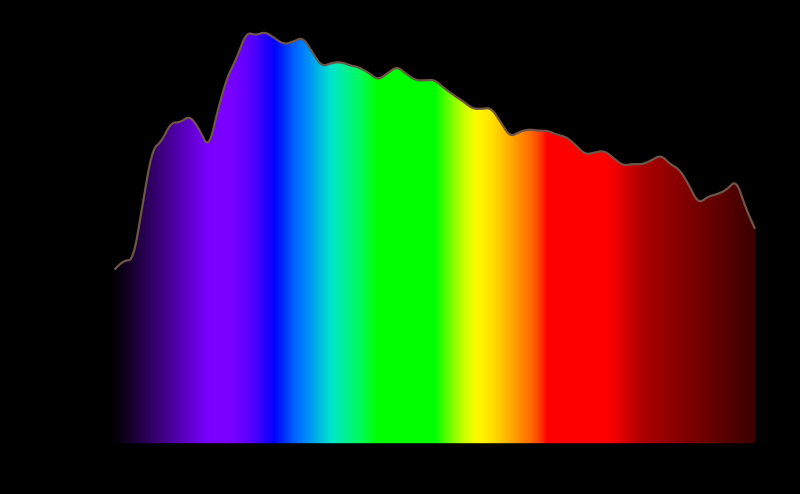

```mathematica
DrawSpectrum[LSD65]
```

```mathematica
DrawCMF[S_,Bk_:Black]:=
ListPlot[Table[{FrequencyRange[[j]],S[[i]][[j]]},{i,1,3,1},{j,1,69,1}],
Background->Black,
PlotStyle->{Red,Green,Blue},
Joined->True,InterpolationOrder->2,
Ticks->{Table[i,{i,380,720,20}]},
ImageSize->gDrawingSize
]
```

### 色匹配函数绘图

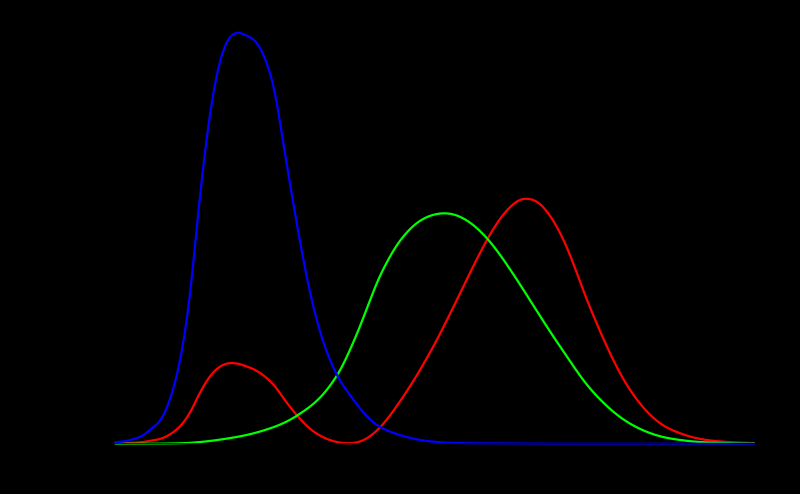

```mathematica
DrawCMF[CMFXYZ]
```

### 色度坐标绘图，目前仅支持xyY、Luv、LUV坐标，可能会重写。

#### CIE 1931 xy的一些工具函数

```mathematica
(*私有函数。此处定义一个各单频光的xyY点集，仅仅方便绘图用,*)
iSpectrumxyY=
XYZ2xyY[#]&/@Transpose[(*20是曝光*)20CMFXYZ];
```

```mathematica
iTemperaturexy=Table[T2xy[x],{x,4000,25000,1000}];
```

```mathematica
(*私有函数。使2D图像变3D。使用时，外面还要套一个Graphics3D*)
iMake3D[plot_,height_,opacity_]:=Module[{newplot},newplot=First@Graphics[plot];
newplot=N@newplot/.{x_?AtomQ,y_?AtomQ}:>{x,y,height};
newplot/.GraphicsComplex[xx__]:>{Opacity[opacity],GraphicsComplex[xx]}]
```

#### CIE 1931 xy色度图绘制：Draw1931_

```mathematica
(*这是一个修修补补用了半年多的函数..画出来还行但代码没法看，所以凑合着使
选项：
PointSize：是数据点大小；
Ymax：是决定可打印数据点的Y的最大值。Y超过该值，便不会打印出来。
Ygamma：该函数的数据点会以真实色彩显现出来，如果数据点过于暗，可以减小该值。相当于对显示亮度作gamma校正。
PlotRange：打印的坐标范围，一般不会改变。
*)
Options[Draw1931xyY]={"PointSize"->0.01,"Ymax"->1,"Ygamma"->1,"PlotRange"->{0,0.9}};
Draw1931xyY[xyYPixels_,OptionsPattern[]]:=Show[
(*被绘制的点集*)
ListPointPlot3D[xyYPixels,
PlotStyle->PointSize[OptionValue["PointSize"]],ColorFunction->Function[{x,y,Y},XYZColor@@Clip0[xyY2XYZ[{x,y,Clip0[Y]^OptionValue["Ygamma"]}]]],ColorFunctionScaling->False],

(*单频光的色点*)
ListPointPlot3D[iSpectrumxyY,ColorFunction->Function[{x,y,Y},XYZColor@@xyY2XYZ[{x,y,Y}]],ColorFunctionScaling->False,PlotStyle->PointSize[0.01]],
(*单频光的轨迹，0.1是曝光*)
Graphics3D[iMake3D[ListPlot[iSpectrumxyY[[All,1;;2]],Joined->True,InterpolationOrder->2,ColorFunction->Function[{x,y},XYZColor@@xyY2XYZ[{x,y,0.1}]]
],0,1]],
(*色温轨迹，0.05是曝光*)
Graphics3D[iMake3D[ListPlot[iTemperaturexy,Joined->True,InterpolationOrder->2,ColorFunction->Function[{x,y},XYZColor@@xyY2XYZ[{x,y,0.05}]]
],0,1]],

(*总绘制函数的设置*)
AxesOrigin->{0,0,0},AxesLabel->{x,y,Y},LabelStyle->Bold,Ticks->None,
Boxed->False,PlotRange->{OptionValue["PlotRange"],OptionValue["PlotRange"],{0,OptionValue["Ymax"]}},
ViewPoint->{0,0,Infinity},ViewVertical->{0,0,1},Background->Black,ImageSize->gDrawingSize]
```

```mathematica
Options[Draw1931XYZ]={"PointSize"->0.01,"Ymax"->1,"Ygamma"->1,"PlotRange"->{0,0.9}};
Draw1931XYZ[XYZPixels_,OptionsPattern[]]:=Show[
(*被绘制的点集*)
ListPointPlot3D[XYZ2xyY/@XYZPixels,
PlotStyle->PointSize[OptionValue["PointSize"]],
ColorFunction->Function[{x,y,Y},XYZColor@@Clip0[xyY2XYZ[{x,y,Clip0[Y]^OptionValue["Ygamma"]}]]],
ColorFunctionScaling->False],

(*单频光的色点*)
ListPointPlot3D[iSpectrumxyY,ColorFunction->Function[{x,y,Y},XYZColor@@xyY2XYZ[{x,y,Y}]],ColorFunctionScaling->False,PlotStyle->PointSize[0.01]],
(*单频光的轨迹，0.1是曝光*)
Graphics3D[iMake3D[ListPlot[iSpectrumxyY[[All,1;;2]],Joined->True,InterpolationOrder->2,ColorFunction->Function[{x,y},XYZColor@@xyY2XYZ[{x,y,0.1}]]
],0,1]],
(*色温轨迹，0.05是曝光*)
Graphics3D[iMake3D[ListPlot[iTemperaturexy,Joined->True,InterpolationOrder->2,ColorFunction->Function[{x,y},XYZColor@@xyY2XYZ[{x,y,0.05}]]
],0,1]],

(*总绘制函数的设置*)
AxesOrigin->{0,0,0},AxesLabel->{x,y,Y},LabelStyle->Bold,Ticks->None,
Boxed->False,PlotRange->{OptionValue["PlotRange"],OptionValue["PlotRange"],{0,OptionValue["Ymax"]}},
ViewPoint->{0,0,Infinity},ViewVertical->{0,0,1},Background->Black,ImageSize->gDrawingSize]
```

```mathematica
(*测试*)Draw1931XYZ[{{1,1,1}}]
```

-Graphics3D-

#### CIE 1976 uv的一些工具函数：

```mathematica
(*此处定义一个各单频光的LUV点集，仅仅方便绘图用*)
iSpectrumLuv=
XYZ2Luv[#]&/@Transpose[(*20是曝光*)20CMFXYZ];
```

```mathematica
iTemperatureLuv=(XYZ2Luv[xyY2XYZ[#]])&/@Table[Append[T2xy[x],1],{x,4000,25000,1000}]
```

{{100,0.223576,0.504918},{100,0.209144,0.488165},{100,0.200737,0.474273},{100,0.195459,0.463242},{100,0.191911,0.454505},{100,0.189405,0.447549},{100,0.187554,0.441928},{100,0.18614,0.43732},{100,0.18503,0.433492},{100,0.184137,0.430273},{100,0.183406,0.427536},{100,0.182798,0.425185},{100,0.182285,0.423148},{100,0.181847,0.421369},{100,0.18147,0.419803},{100,0.181141,0.418416},{100,0.180852,0.41718},{100,0.180597,0.416072},{100,0.18037,0.415074},{100,0.180167,0.414171},{100,0.179984,0.413351},{100,0.179819,0.412602}}

```mathematica
Options[Draw1976XYZ]={"refWP"->"E","PointSize"->0.01,"Lmax"->100,"Lgamma"->1};
Draw1976XYZ[XYZPixels_,OptionsPattern[]]:=Show[
(*被绘制的点集*)
ListPointPlot3D[XYZ2Luv[#]&/@XYZPixels,
PlotStyle->PointSize[OptionValue["PointSize"]],ColorFunction->Function[{L,u,v},LUVColor@@Luv2LUV[{(L/100)^OptionValue["Lgamma"],u,v},"refWP"->OptionValue["refWP"]]],ColorFunctionScaling->False],
(*单频光的色点*)
ListPointPlot3D[iSpectrumLuv,ColorFunction->Function[{L,u,v},LUVColor@@Luv2LUV[{0.8,u,v},"refWP"->OptionValue["refWP"]]],ColorFunctionScaling->False,PlotStyle->PointSize[0.01]],
(*某亮度下（L=0.3），单频光的轨迹*)
Graphics3D[Rotate[iMake3D[ListPlot[iSpectrumLuv[[All,2;;3]],Joined->True,InterpolationOrder->2,ColorFunction->Function[{u,v},LUVColor@@Luv2LUV[{0.2,u,v},"refWP"->OptionValue["refWP"]]]
],0,1],120Degree,{1,1,1}]],
(*色温轨迹，0.05是曝光*)
Graphics3D[Rotate[iMake3D[ListPlot[iTemperatureLuv[[All,2;;3]],Joined->True,InterpolationOrder->2,ColorFunction->Function[{u,v},LUVColor@@Luv2LUV[{0.2,u,v},"refWP"->OptionValue["refWP"]]]
],0,1],120Degree,{1,1,1}]],
(*总绘制函数的设置*)
AxesOrigin->{0,0,0},AxesLabel->{L,"u'","v'"},LabelStyle->Bold,Ticks->None,
Boxed->False,PlotRange->{{0,OptionValue["Lmax"]},{0,0.7},{0,0.6}},BoxRatios->{2,7,6},
ViewPoint->{Infinity,0,0},ViewVertical->{1,0,0},Background->Black,ImageSize->gDrawingSize]
```

```mathematica
(*测试*)Draw1976XYZ[{{1,1,1}}]
```

-Graphics3D-

```mathematica
Options[iDraw1976XYZWithoutSpectrum]={"refWP"->"E","PointSize"->0.01,"Lmax"->100,"Lgamma"->1};
iDraw1976XYZWithoutSpectrum[XYZPixels_,OptionsPattern[]]:=Show[
(*被绘制的点集*)
ListPointPlot3D[XYZ2Luv[#]&/@XYZPixels,
PlotStyle->PointSize[OptionValue["PointSize"]],ColorFunction->Function[{L,u,v},LUVColor@@Luv2LUV[{(L/100)^OptionValue["Lgamma"],u,v},"refWP"->OptionValue["refWP"]]],ColorFunctionScaling->False],
(*总绘制函数的设置*)
AxesOrigin->{0,0,0},AxesLabel->{L,"u'","v'"},LabelStyle->Bold,Ticks->None,
Boxed->False,PlotRange->{{0,OptionValue["Lmax"]},{0,0.7},{0,0.6}},BoxRatios->{2,7,6},
ViewPoint->{Infinity,0,0},ViewVertical->{1,0,0},Background->Black,ImageSize->gDrawingSize]
```

```mathematica
Options[Draw1976Compare]={"refWP"->"E","PointSize"->0.01,"Lmax"->100,"Lgamma"->1,"SizeRatio"->0.8};
Draw1976Compare[XYZPixels1_,XYZPixels2_,OptionsPattern[]]:=Module[{l},
l=Min[Length[XYZPixels1],Length[XYZPixels2]];
Show[
Draw1976XYZ[XYZPixels1,
"refWP"->OptionValue["refWP"],
"PointSize"->OptionValue["PointSize"],
"Lmax"->OptionValue["Lmax"],
"Lgamma"->OptionValue["Lgamma"]
],
iDraw1976XYZWithoutSpectrum[XYZPixels2,
"refWP"->OptionValue["refWP"],
"PointSize"->(OptionValue["PointSize"]*OptionValue["SizeRatio"]),
"Lmax"->OptionValue["Lmax"],
"Lgamma"->OptionValue["Lgamma"]
],
Graphics3D[{White,Line[Table[{XYZ2Luv[XYZPixels1[[x]]],XYZ2Luv[XYZPixels2[[x]]]},{x,1,l}]]}]
]
]
```